## 3.029 Spring 2022 Lecture 19 - 04/11/2022

## Statistical Mechanics I

Ludwig Boltzmann, who spent much of his life studying statistical mechanics, died in 1906, by his own hand. 
Paul Ehrenfest, carrying on the work, died similarly in 1933. Now it is our turn to study statistical mechanics. 
Perhaps it will be wise to approach the subject cautiously.
																	David Louis Goodstein

## Statistical Ensembles

Statistical mechanics is a probabilistic approach to equilibrium macroscopic properties of large # of degrees of freedom.

We already know how to describe equilibrium properties at the macro-scale → Thermodynamics!

Macro-state, M :	Described by a few Thermodynamic variables

Statistical mechanics studies ensembles of micro-states, corresponding to a given macro-state

Micro-state, μ : 		Described by a large number of degrees of freedom

Instead of averaging the “mechanical” variables over time, we postulate that, given sufficient time, the “mechanical” variable will evolve through all the possible microscopic states

Thus an average over a large number of possible microscopic states, i.e. an ensemble average, can be used instead

The second postulate of statistical mechanics states that microstates in ensembles are distributed uniformly

I.e. each microstate has the same probability of occurring

Together the two postulates form the ergodicity hypothesis

A system would spend the same amount of time in each microstate over a long time

### Thermodynamic Potentials Reminder

Recall that we can recast the fundamental thermodynamic relation

In more natural variables, depending on the experimental conditions we’re interested in

Entropy

its natural variables are:

Internal Energy, U

Volume,

Mole numbers,

Helmholtz free energy

its natural variables are:

Temperature, T

Volume,

Mole numbers,

Gibbs free energy

its natural variables are:

Temperature, T

Pressure, P

Mole numbers,

Grand energy

its natural variables are:

Temperature, T

Volume, V

Chemical potentials,

Each thermodynamic potential corresponds to a particular statistical ensemble

The two most important ones we’ll study are:

Entropy 			→ 		Microcanonical ensemble, aka NVE

Helmholtz Free Energy 		→ 		Canonical ensemble, aka NVT

## The Microcanonical Ensemble

As we mentioned above, this corresponds to an isolated system

I.e. no work or heat is performed

This fixes the internal energy of the system

Since the total internal energy is conserved, all the microstates are confined on this constant-E surface

The probability of observing a particular microstate is then given by

p_(𝒰, V, N)(μ)=1/(Ω(𝒰, V, N))Piecewise[{{1, for E(μ)=𝒰}, {0, otherwise}}]

Where Ω(𝒰, V, N) is the “degeneracy” or the surface area of the constant-energy surface

### Infinite Stair-Case

Consider N non-interacting particles on an infinite staircase “potential” of the form

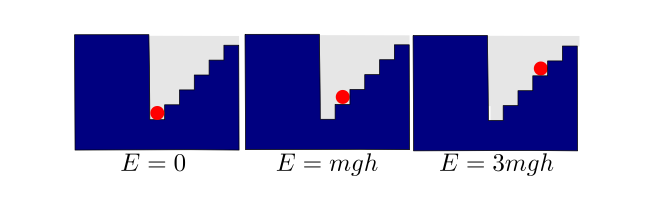

Each particle, i can be in any energy state

And we fix the total internal energy of the system

How many different ways can we arrange N particles to have the same total internal energy?

We’ll work with normalized units (mgh=1)

This can be formulated as a Frobenius Equation

a_1 x_1+...+a_n x_n=b

where we set all the weight coefficients α_i to 1

```mathematica
With[{internalEnergy=5,numberOfParticles=3},
FrobeniusSolve[ConstantArray[1,numberOfParticles],internalEnergy]
]
%//Length
```

{{0,0,5},{0,1,4},{0,2,3},{0,3,2},{0,4,1},{0,5,0},{1,0,4},{1,1,3},{1,2,2},{1,3,1},{1,4,0},{2,0,3},{2,1,2},{2,2,1},{2,3,0},{3,0,2},{3,1,1},{3,2,0},{4,0,1},{4,1,0},{5,0,0}}

21

This returns a list of the stair number (or energy level) each particle is sitting at

E.g. the first result says that the first two particles are sitting at the ground-level (with zero energy), and the third particle is at the 5^th rung

This is actually a known problem in combinatorics, called the "stars and bars" problem

Consider having U balls, and having to distribute them in N slots, i.e. using N-1 partitions

Let’s “Brute-Force” it as a start

```mathematica
randomBallsNBars[numberOfBalls_,numberOfBins_]:=Block[{
partitions=RandomChoice[Range[0,numberOfBalls],numberOfBins-1],
balls=Tuples[{Range[numberOfBalls],{0}}]},
partitions=Flatten[Take[Subdivide[#[[1]]-1/4,#[[1]]+1/4,Length[#]+1],{2,-2}]&/@Union[Gather[partitions]]];
Graphics[{
Disk[#,1/4]&/@balls,
Red,Thick,Line[{{#+1/2,-1/4},{#+1/2,1/4}}]&/@partitions
},PlotRange->{{1/4,numberOfBalls+3/4},All}]]
```

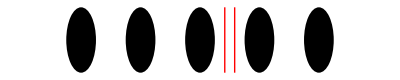

```mathematica
randomBallsNBars[5,3]
```

We’ll generate very many random instances above, and find the unique ones

21

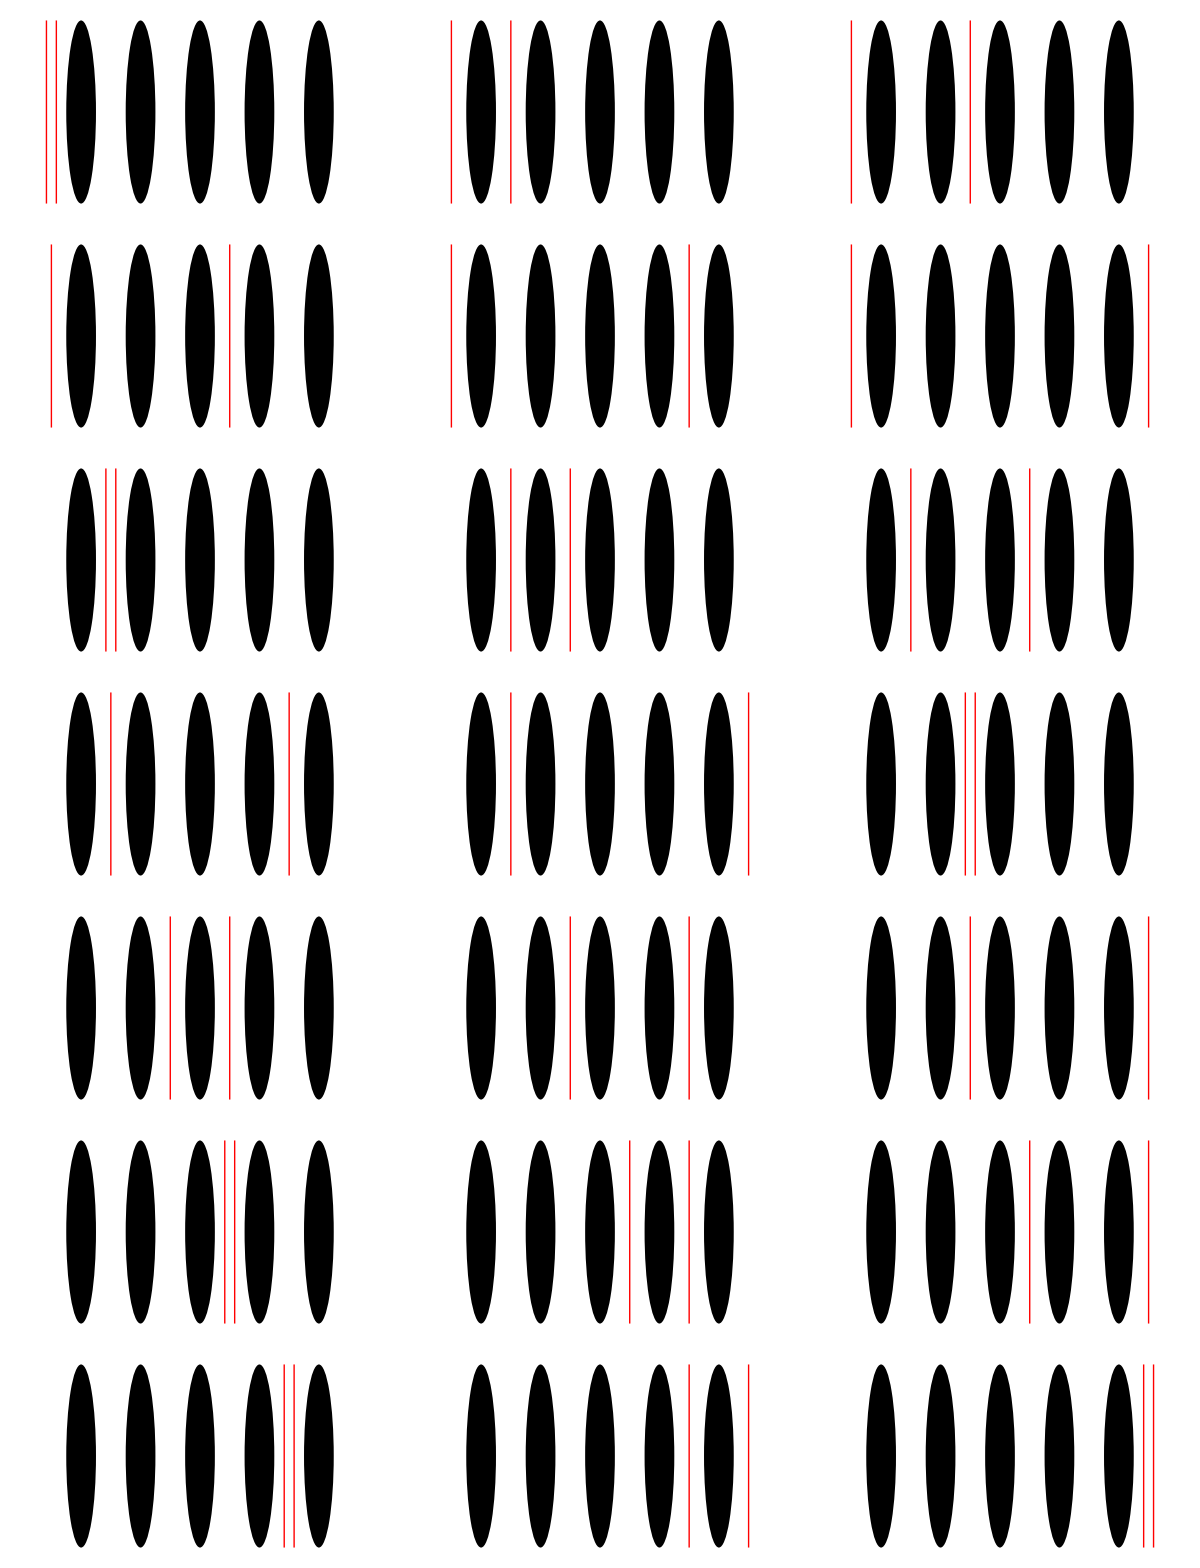

```mathematica
Block[{U=5,m=3,unique},
unique=Union[Table[randomBallsNBars[U,m],1000]];
Echo[Length[unique]];
Multicolumn[unique,3,Frame->All,Appearance->"Horizontal"]
]
```

This indeed returns the same number of configurations!

But the “Brute-force” approaches above will become quite cumbersome

Fortunately, there’s a closed-form solution of the combinatorics above, given by the Binomial coefficient: (U+N-1
U)

```mathematica
FunctionExpand[Binomial[U+N-1,U]]
%/.Gamma[a_]:>(a-1)!
```

Gamma[N+U]/(Gamma[N] Gamma[1+U])

((-1+N+U)!)/((-1+N)! U!)

As we saw before, Mathematica keeps Binomial coefficients using the generalized Gamma function,  Γ(n) = (n-1)!

So we’ll simply write out own

```mathematica
binomial[n_,k_]:=ExpandAll[(n!)/((n-k)!k!)]
```

```mathematica
binomial[U+N-1,U]
```

((-1+N+U)!)/((-1+N)! U!)

We conclude that the degeneracy is given by

### “Partition Functions” & Thermodynamic Potentials

We called the result above, the “degeneracy” of the constant-Energy surface

In a more general sense, we can refer to this as a “partition function” for the ensemble’s natural variables

The connection between the ensemble’s “partition function” and the relevant thermodynamic potential (Entropy) is given by Boltzmann’s famous equation

The form of this equation is physically-motivated as-follows:

Entropy is a extensive thermodynamics quantity and should scale (linearly) with the size of the system

The number of configurations of two independent systems should be the product of the numbers of configuration of each sub-system

A log-function indeed achieves these requirements!

```mathematica
infiniteStaircaseEntropy["exact"][U_,n_]=Log[binomial[U+n-1,U]]
```

Log[((-1+n+U)!)/((-1+n)! U!)]

Let’s plot the entropy for 100 non-interacting particles as  a function of the internal energy

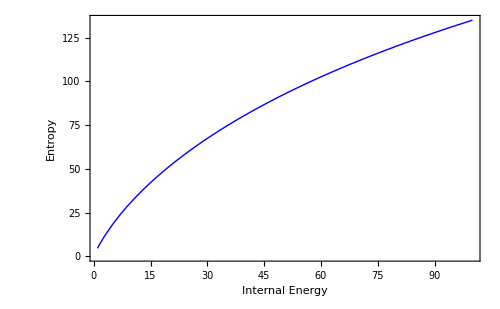

```mathematica
Plot[infiniteStaircaseEntropy["exact"][U,100],{U,1,100},PlotStyle->Directive[Blue,Thick],Frame->True,LabelStyle->Directive[Black,Thick,16],ImageSize->500,FrameLabel->{"Internal Energy","Entropy"}]
```

As we saw when we introduced the regular solution model, it’s often convenient to simplify this expression in the Thermodynamic limit using Stirling’s approximation

```mathematica
stirlingsApproximation={
Log[n_!]:>n Log[n]-n,
Log[a_/b_]:>Log[a]-Log[b],
Log[a_*b_]:>Log[a]+Log[b]
};
```

```mathematica
infiniteStaircaseEntropy["approximate"][U_,n_]=infiniteStaircaseEntropy["exact"][U,n]//.stirlingsApproximation
```

-((-1+n) Log[-1+n])-U Log[U]+(-1+n+U) Log[-1+n+U]

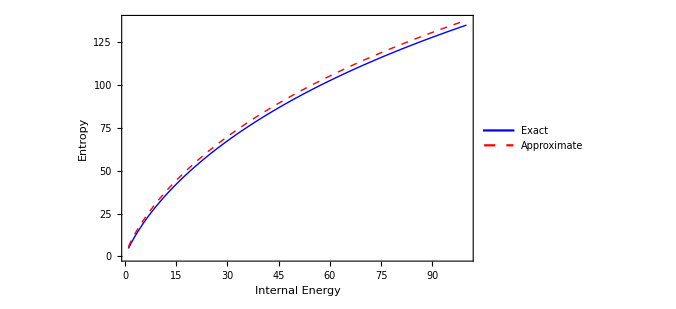

```mathematica
Plot[{infiniteStaircaseEntropy["exact"][U,100],infiniteStaircaseEntropy["approximate"][U,100]},{U,1,100},PlotStyle->{Directive[Blue,Thick],Directive[Red,Dashed,Thick]},Frame->True,LabelStyle->Directive[Black,Thick,16],ImageSize->500,FrameLabel->{"Internal Energy","Entropy"},PlotLegends->Placed[{"Exact","Approximate"},{0.75,0.25}]]
```

Once we have an expression for the thermodynamic potential of interest, we can use its differential form to obtain other thermodynamically-relevant quantities

E.g. the temperature can be obtained as:

```mathematica
infiniteStaircaseInverseTemperature["exact"][U_,n_]=FullSimplify[Derivative[1,0][infiniteStaircaseEntropy["exact"]][U,n],{U,n}>0]
infiniteStaircaseInverseTemperature["approximate"][U_,n_]=FullSimplify[Derivative[1,0][infiniteStaircaseEntropy["approximate"]][U,n],{U,n}>0]
```

-HarmonicNumber[U]+HarmonicNumber[-1+n+U]

-Log[U]+Log[-1+n+U]

We can “invert” this expression to give the internal energy as a function of temperature

```mathematica
infiniteStaircaseInternalEnergy["approximate"][T_,n_]=First[SolveValues[infiniteStaircaseInverseTemperature["approximate"][U,n]==1/T,U]]
```

(-1+n)/(-1+ⅇ^(1/T))

Finally, the constant-volume heat-capacity is given by

```mathematica
infiniteStaircaseHeatCapacity["approximate"][T_,n_]=Derivative[1,0][infiniteStaircaseInternalEnergy["approximate"]][T,n]
```

(ⅇ^(1/T) (-1+n))/((-1+ⅇ^(1/T))^2 T^2)

The molar heat capacity in the thermodynamic limit is then given by

```mathematica
infiniteStaircaseMolarHeatCapacity["approximate"][T_]=Limit[infiniteStaircaseHeatCapacity["approximate"][T,n]/n,n->∞]
```

ⅇ^(1/T)/(T^2-2 ⅇ^(1/T) T^2+ⅇ^(2/T) T^2)

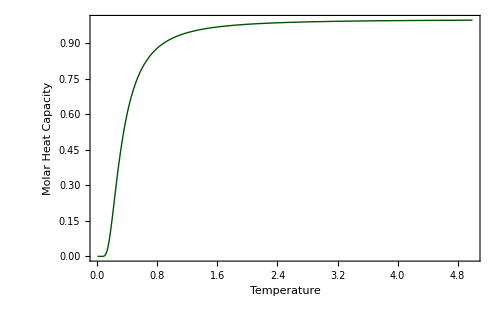

```mathematica
Plot[infiniteStaircaseMolarHeatCapacity["approximate"][T],{T,0,5},PlotStyle->Directive[RGBColor[0,1/3,0],Thick],Frame->True,LabelStyle->Directive[Black,Thick,16],ImageSize->500,FrameLabel->{"Temperature","Molar Heat Capacity"},PlotRange->All]
```

There’s two important features in this plot:

The heat capacity approaches zero as T → 0

This is a common feature for all systems in which the first excited state is separated in energy from the ground state (i.e. all discrete energy level systems)

The heat capacity saturates as T → ∞, i.e. in the ‘classical’ limit

## The Canonical Ensemble

In the canonical ensemble, the macro-states allow heat into the system, but no external work.

The system can therefore be held at constant temperature by being in contact with a (large) reservoir to transfer heat to and from.

If it helps, you can think of the whole setup (system + reservoir) as a microcanonical ensemble

p(μ_S⊗μ_R)=1/(Ω_(S⊕R))Piecewise[{{1, for E_S(μ_S)+E_R(μ_R)=𝒰}, {0, otherwise}}]

The probability of observing a particular microstate in the system can then be obtained by ‘summing over’ all reservoir microstates.

p(μ_S)=∑_{μ_R} p_(𝒰, V, N)(μ_S⊗μ_R)

Once we pick a microstate of the system, then all available reservoir micro-states are given by the degeneracy of the reservoir with the remaining energy

p(μ_S)=(Ω_R(𝒰-E_S(μ_S)))/(Ω_(S⊕R)(𝒰))∝ Exp[1/k_B S_R(𝒰-E_S(μ_S))]

For the reservoir to be an effective  heat bath, the system energy must be small compared to that of the reservoir

As such we may approximate the entropy as

S_R(𝒰-E_S(μ_S))≃ S_R(𝒰)-E_S(μ_S)(∂ S_R)/(∂E_R)=S_R(𝒰)-(E_S(μ_S))/T

Which gives the system’s microstate probability as:

p(μ)=Exp[-(E(μ))/T]/ Z(T,V,{N})

where, Z is the ensemble’s “partition function”

Z(T,V,{N}) = ∑_{μ} Exp[-E(μ)/T]

Note: Z is often referred to as simply the partition function, but as we’ve seen there is in-fact a “partition function” for each ensemble, so Z is better called the “canonical partition function”

### (Finite) Stair-Case Revisited

We’ll revisit the same problem using the canonical ensemble

We imagine having N particles in contact with a thermal reservoir at some temperature

Occasionally, the particles interact with the bath, decreasing or increasing their energy state

The partition function is given by

We’ll again use normalized units and define a temperature τ=(K_B T)/mgh

Z=∑_(i=0)^nMax Exp[-E_i/k_BT] =∑_(n=0)^nMax Exp[-n/τ]

```mathematica
staircaseCanonicalPartitionFunctionSingle["finite"][τ_,nMax_]=FullSimplify[Sum[Exp[-i/τ],{i,0,nMax}] ,{τ,nMax}>0]
```

(ⅇ^(-nMax/τ) (-1+ⅇ^((1+nMax)/τ)))/(-1+ⅇ^(1/τ))

We’ve kept the staircase finite to investigate a curious phenomenon later on

To compare with our results from the microcanonical ensemble, let’s also take the limit of n_max→ ∞

```mathematica
staircaseCanonicalPartitionFunctionSingle["infinite"][τ_]=FullSimplify[Limit[staircaseCanonicalPartitionFunctionSingle["finite"][τ,nMax] ,nMax->∞],τ>0]
```

1+1/(-1+ⅇ^(1/τ))

This is the partition function for a single particle

Since the particles are non-interacting (and distinguishable) we can simply write

Z_N= Z_1^N

```mathematica
staircaseCanonicalPartitionFunction["finite"][τ_,nMax_,n_]=(staircaseCanonicalPartitionFunctionSingle["finite"][τ,nMax])^n;
staircaseCanonicalPartitionFunction["infinite"][τ_,n_]=(staircaseCanonicalPartitionFunctionSingle["infinite"][τ])^n;
```

As we saw above, the ensemble’s partition function is related to the relevant thermodynamic potential

For the canonical ensemble this gives the Helmholtz Free energy as

```mathematica
staircaseHelmholtzFreeEnergy["finite"][τ_,nMax_,n_]=- τ Log[staircaseCanonicalPartitionFunction["finite"][τ,nMax,n]];
staircaseHelmholtzFreeEnergy["infinite"][τ_,n_]=- τ Log[staircaseCanonicalPartitionFunction["infinite"][τ,n]];
```

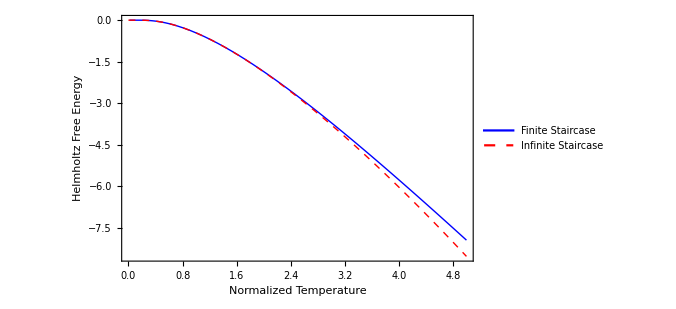

```mathematica
Quiet@Plot[{staircaseHelmholtzFreeEnergy["finite"][τ,10,1],staircaseHelmholtzFreeEnergy["infinite"][τ,1]},{τ,0,5},PlotStyle->{Directive[Blue,Thick],Directive[Red,Dashed,Thick]},Frame->True,LabelStyle->Directive[Black,Thick,16],ImageSize->500,FrameLabel->{"Normalized Temperature","Helmholtz Free Energy"},PlotLegends->Placed[{"Finite Staircase","Infinite Staircase"},{0.75,0.75}]]
```

We can now use the differential form of the Helmholtz free energy to extract other thermodynamic potentials

Entropy

```mathematica
staircaseCanonicalEntropy["finite"][τ_,nMax_,n_]=FullSimplify[- Derivative[1,0,0][staircaseHelmholtzFreeEnergy["finite"]][τ,nMax,n],{τ,nMax,n}>0];
staircaseCanonicalEntropy["infinite"][τ_,n_]=FullSimplify[- Derivative[1,0][staircaseHelmholtzFreeEnergy["infinite"]][τ,n],{τ,n}>0];
```

Internal Energy

```mathematica
staircaseCanonicalInternalEnergy["finite"][τ_,nMax_,n_]= FullSimplify[staircaseHelmholtzFreeEnergy["finite"][τ,nMax,n]+ τ staircaseCanonicalEntropy["finite"][τ,nMax,n], Assumptions->{τ,nMax,n}>0]
staircaseCanonicalInternalEnergy["infinite"][τ__,n_]= FullSimplify[staircaseHelmholtzFreeEnergy["infinite"][τ,nMax,n]+ τ staircaseCanonicalEntropy["infinite"][τ,n], Assumptions->{τ,n}>0]
```

n (1/(-1+ⅇ^(1/τ))-(1+nMax)/(-1+ⅇ^((1+nMax)/τ)))

n/(-1+ⅇ^(1/τ))

Note that the infinite result compares quite nicely with our approximate internal result in the microcanonical ensemble

The slight difference is due to Stirling’s approximation and negligible as n→∞

```mathematica
infiniteStaircaseInternalEnergy["approximate"][T,n]
```

(-1+n)/(-1+ⅇ^(1/T))

Heat Capacity

```mathematica
staircaseCanonicalMolarHeatCapacity["finite"][τ_,nMax_]=Limit[Derivative[1,0,0][staircaseCanonicalInternalEnergy["finite"]][τ,nMax,n]/n,n->∞]
staircaseCanonicalMolarHeatCapacity["infinite"][τ_]=Limit[Derivative[1,0][staircaseCanonicalInternalEnergy["infinite"]][τ,n]/n,n->∞]
```

ⅇ^(1/τ)/((-1+ⅇ^(1/τ))^2 τ^2)-(ⅇ^((1+nMax)/τ) (1+nMax)^2)/((-1+ⅇ^((1+nMax)/τ))^2 τ^2)

ⅇ^(1/τ)/((-1+ⅇ^(1/τ))^2 τ^2)

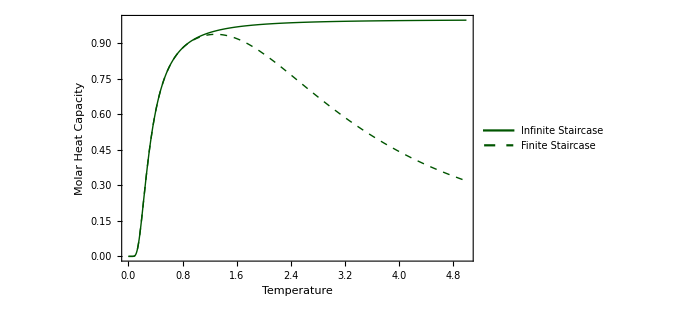

```mathematica
Quiet@Plot[{
staircaseCanonicalMolarHeatCapacity["infinite"][τ],
staircaseCanonicalMolarHeatCapacity["finite"][τ,10]
},{τ,0,5},PlotStyle->{Directive[RGBColor[0,1/3,0],Thick],Directive[RGBColor[0,1/3,0],Dashed,Thick]},Frame->True,LabelStyle->Directive[Black,Thick,16],ImageSize->500,FrameLabel->{"Temperature","Molar Heat Capacity"},PlotRange->All,PlotLegends->Placed[{"Infinite Staircase","Finite Staircase"},{0.775,0.225}]]
```

In addition to the vanishing molar heat capacity as Τ→0, there’s another really important feature to this plot

The molar heat capacity for the finite staircase also vanishes at T→∞

This is true for all systems with a saturating number of states as a function of energy

### Negative Temperatures (?)

Because our system is finite, there is a limited amount of energy that can be transferred to the system

As more and more energy gets transferred, there is a point at which the number of possible states starts decreasing

Since the temperature is given by

We will plot the entropy vs the internal energy parametrically

If the slope is negative, so will the temperature

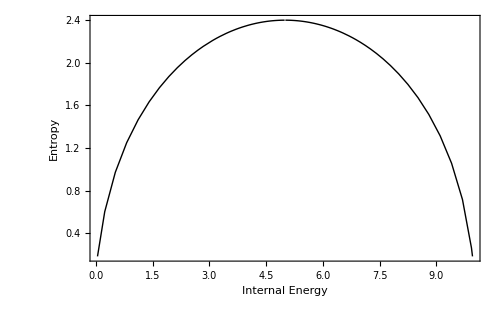

```mathematica
ParametricPlot[{staircaseCanonicalInternalEnergy["finite"][τ,10,1],staircaseCanonicalEntropy["finite"][τ,10,1]},{τ,-1000,1000},AspectRatio->1/GoldenRatio,PlotRange->All,Frame->True,PlotStyle->Directive[Black,Thick],ImageSize->500,PlotPoints->100,LabelStyle->Directive[Black,Thick,18],FrameLabel->{"Internal Energy","Entropy"}]
```